```mathematica
f1=(YR1s-YR2s)/(YR1-YR2)
f2=(YTmax-YTmin)/(YMmax-YMmin)
Again=f2 (YR1s-YR2s)
Aoffs=YTmax-Again (YMmax-YR1s)/(YR1s-YR2s)
Yout=Again (Ypix-YR1)/(YR1-YR2)+Aoffs
```

(YR1s-YR2s)/(YR1-YR2)

(YTmax-YTmin)/(YMmax-YMmin)

((YR1s-YR2s) (YTmax-YTmin))/(YMmax-YMmin)

YTmax-((YMmax-YR1s) (YTmax-YTmin))/(YMmax-YMmin)

YTmax-((YMmax-YR1s) (YTmax-YTmin))/(YMmax-YMmin)+((Ypix-YR1) (YR1s-YR2s) (YTmax-YTmin))/((YMmax-YMmin) (YR1-YR2))

```mathematica
Yout=f1 f2 (Ypix-YR1)-f2 (YMmax-YR1s)+YTmax
Yout/.{YR1->YR1s,YR2->YR2s,Ypix->YMmin}//Simplify
Yout/.{YR1->YR1s,YR2->YR2s,Ypix->YMmax}//Simplify
Yout/.{YR1->YR1s,YR2->YR2s,Ypix->(YMmin+YMmax)/2}//Simplify
```

YTmax-((YMmax-YR1s) (YTmax-YTmin))/(YMmax-YMmin)+((Ypix-YR1) (YR1s-YR2s) (YTmax-YTmin))/((YMmax-YMmin) (YR1-YR2))

YTmin

YTmax

(YTmax+YTmin)/2

```mathematica
sf1=D[Yout,YR1s]//Simplify
```

((Ypix-YR2) (YTmax-YTmin))/((YMmax-YMmin) (YR1-YR2))

```mathematica
sf2=D[Yout,YR2s]//Simplify
```

-((Ypix-YR1) (YTmax-YTmin))/((YMmax-YMmin) (YR1-YR2))

```mathematica
sf3=D[Yout,YR1]//Simplify
```

-((Ypix-YR2) (YR1s-YR2s) (YTmax-YTmin))/((YMmax-YMmin) (YR1-YR2)^2)

```mathematica
sf4=D[Yout,YR2]//Simplify
```

((Ypix-YR1) (YR1s-YR2s) (YTmax-YTmin))/((YMmax-YMmin) (YR1-YR2)^2)

```mathematica
sf5=D[Yout,YMmin]
```

-((YMmax-YR1s) (YTmax-YTmin))/(YMmax-YMmin)^2+((Ypix-YR1) (YR1s-YR2s) (YTmax-YTmin))/((YMmax-YMmin)^2 (YR1-YR2))

```mathematica
sf6=D[Yout,YMmax]
```

-(YTmax-YTmin)/(YMmax-YMmin)+((YMmax-YR1s) (YTmax-YTmin))/(YMmax-YMmin)^2-((Ypix-YR1) (YR1s-YR2s) (YTmax-YTmin))/((YMmax-YMmin)^2 (YR1-YR2))

```mathematica
sf7=D[Yout,Ypix]
```

((YR1s-YR2s) (YTmax-YTmin))/((YMmax-YMmin) (YR1-YR2))

## M1k

```mathematica
sf1fn[YR1_,YR1s_,YR2_,YR2s_,YMmin_,YMmax_,YTmin_,YTmax_,Ypix_]=sf1;
sf2fn[YR1_,YR1s_,YR2_,YR2s_,YMmin_,YMmax_,YTmin_,YTmax_,Ypix_]=sf2;
sf3fn[YR1_,YR1s_,YR2_,YR2s_,YMmin_,YMmax_,YTmin_,YTmax_,Ypix_]=sf3;
sf4fn[YR1_,YR1s_,YR2_,YR2s_,YMmin_,YMmax_,YTmin_,YTmax_,Ypix_]=sf4;
sf5fn[YR1_,YR1s_,YR2_,YR2s_,YMmin_,YMmax_,YTmin_,YTmax_,Ypix_]=sf5;
sf6fn[YR1_,YR1s_,YR2_,YR2s_,YMmin_,YMmax_,YTmin_,YTmax_,Ypix_]=sf6;
sf7fn[YR1_,YR1s_,YR2_,YR2s_,YMmin_,YMmax_,YTmin_,YTmax_,Ypix_]=sf7;
```

```mathematica
q1=sf1fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q2=sf2fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q3=sf3fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q4=sf4fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q5=sf5fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q6=sf6fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q7=sf7fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
uYpix=1.7;
uYMmin=1.7/Sqrt[64];
uYMmax=1.7/Sqrt[64];
uYR1=uYR1s=uYR2=uYR2s=1.7/Sqrt[120];
Clear[u]
u[Ypix_]=Sqrt[(q1 uYR1s)^2+(q2 uYR2s)^2+(q3 uYR1)^2+(q4 uYR2)^2+(q5 uYMmin)^2+(q6 uYMmax)^2+(q7 uYpix)^2];
```

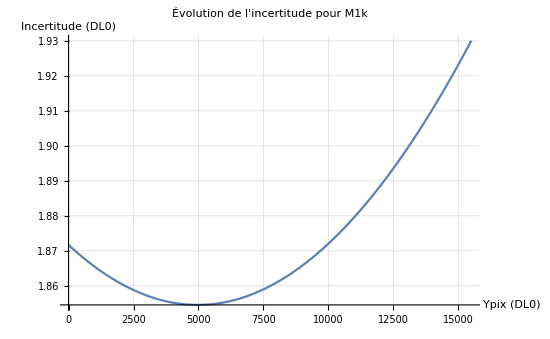

```mathematica
Plot[u[yPix],{yPix,0,15500},GridLines->Automatic,AxesLabel->{"Ypix (DL0)","Incertitude (DL0)"},PlotLabel->"Évolution de l'incertitude pour M1k"]
```

```mathematica
q1max=sf1fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q2max=sf2fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q3max=sf3fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q4max=sf4fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q5max=sf5fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q6max=sf6fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q7max=sf7fn[7800.0,7800.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
u[15500]
```

2.2058

-1.12481

-2.2058

1.12481

-1.11022×10^-16

-1.08099

1.08099

1.93006

## M2kUD

```mathematica
q1=sf1fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q2=sf2fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q3=sf3fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q4=sf4fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q5=sf5fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q6=sf6fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
q7=sf7fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,Ypix];
uYpix=1.7;
uYMmin=1.7/Sqrt[64];
uYMmax=1.7/Sqrt[64];
uYR1=uYR1s=uYR2=uYR2s=1.7/Sqrt[120];
Clear[u]
u[Ypix_]=Sqrt[(q1 uYR1s)^2+(q2 uYR2s)^2+(q3 uYR1)^2+(q4 uYR2)^2+(q5 uYMmin)^2+(q6 uYMmax)^2+(q7 uYpix)^2];
```

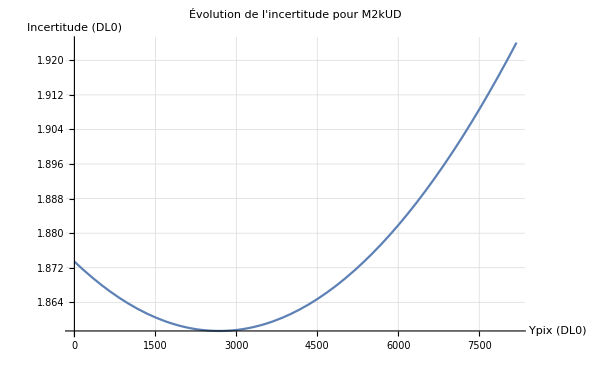

```mathematica
Plot[u[yPix],{yPix,0,8191},GridLines->Automatic,AxesLabel->{"Ypix (DL0)","Incertitude (DL0)"},PlotLabel->"Évolution de l'incertitude pour M2kUD"]
```

```mathematica
q1max=sf1fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,8191]
q2max=sf2fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,8191]
q3max=sf3fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,8191]
q4max=sf4fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,8191]
q5max=sf5fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,8191]
q6max=sf6fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,8191]
q7max=sf7fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,8191]
u[8191]
```

2.21631

-1.13532

-2.21631

1.13532

-0.556403

-0.524583

1.08099

1.92409

```mathematica
q1max=sf1fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q2max=sf2fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q3max=sf3fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q4max=sf4fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q5max=sf5fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q6max=sf6fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
q7max=sf7fn[4200.0,4200.0,400.0,400.0,1300.0,15500.0,650,16000,15500]
u[15500]
```

4.2955

-3.21451

-4.2955

3.21451

0.

-1.08099

1.08099

2.1946